#### Метод Рунге - Кутты для решения задачи Коши для однородного дифференциального уравнения 1 - го порядка

```mathematica
(*http: //mathprofi.ru/metody_eilera _i _runge _kutty.html*)
```

Euler Method

```mathematica
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[x, 0]=0;
z'[x_,z_]:=-z+a*x;
Subscript[z, 0]=α;
h=0.1;
```

```mathematica
Do[Subscript[x, i]=Subscript[x, i-1]+h,{i,1,10}];
Do[Subscript[y, i]=Subscript[y, i-1]+h*y'[Subscript[x, i-1],Subscript[y, i-1]],{i,1,10}];
Do[Subscript[z, i]=Subscript[z, i-1]+h*z'[Subscript[x, i-1],Subscript[y, i-1]],{i,1,10}];
Subscript[z, 0] = Solve[Subscript[z, 6]==Subscript[y, 6]][[1,1,2]];
Do[Subscript[z, i]=Subscript[z, i-1]+h*z'[Subscript[x, i-1],Subscript[y, i-1]],{i,1,10}];
```

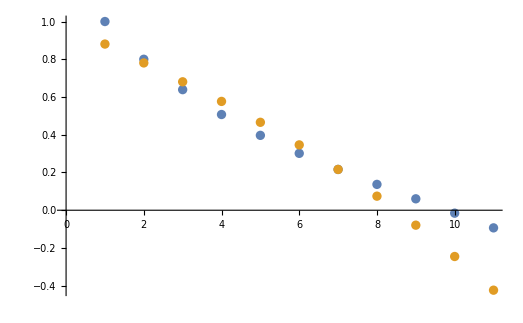

0.880563

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,10}],Table[Subscript[z, i],{i,0,10}]}]
Print[Subscript[z, 0]]
```

Euler Cachy Method

```mathematica
Do[Unset[Subscript[y, i]],{i,0,10}]
Do[Unset[Subscript[z, i]],{i,0,10}]
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[ỹ, 0]=Subscript[y, 0];
Subscript[x, 0]=0;
z'[x_,z_]:=-z+a*x;
Subscript[z, 0]=α;
Subscript[z̃, 0]=Subscript[z, 0];
h=0.1;
```

```mathematica
For[i=1,i≤10,i++,
Subscript[ỹ, i]=Subscript[y, i-1]+h*y'[Subscript[x, i-1],Subscript[y, i-1]];
Subscript[y, i]=Subscript[y, i-1]+0.5*h(y'[Subscript[x, i-1],Subscript[y, i-1]] + y'[Subscript[x, i],Subscript[ỹ, i]]);
];
For[i=1,i≤6,i++,
Subscript[z̃, i]=Subscript[z, i-1]+h*z'[Subscript[x, i-1],Subscript[z, i-1]];
Subscript[z, i]=Subscript[z, i-1]+0.5*h(z'[Subscript[x, i-1],Subscript[z, i-1]] + z'[Subscript[x, i],Subscript[z̃, i]]);
];
```

```mathematica
Subscript[z, 0]=Solve[Subscript[z, 6]==Subscript[y, 6]][[1,1,2]];
Subscript[z̃, 0]=Subscript[z, 0];
For[i=1,i≤10,i++,
Subscript[z̃, i]=Subscript[z, i-1]+h*z'[Subscript[x, i-1],Subscript[z, i-1]];
Subscript[z, i]=Subscript[z, i-1]+0.5*h(z'[Subscript[x, i-1],Subscript[z, i-1]] + z'[Subscript[x, i],Subscript[z̃, i]]);
];
```

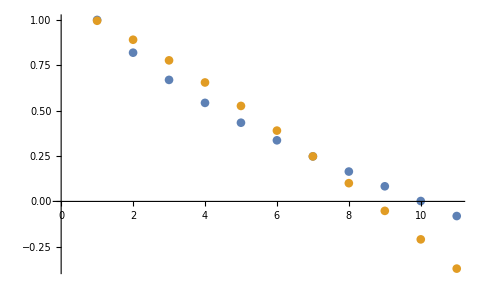

0.995411

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,10}],Table[Subscript[z, i],{i,0,10}]}]
Print[Subscript[z, 0]]
```

Traditional Runge Kutta Method

```mathematica
Do[Unset[Subscript[y, i]],{i,0,10}]
Do[Unset[Subscript[z, i]],{i,0,10}]
a = -2;
y'[x_,y_]:= a * y - x^2;
Subscript[y, 0]=1;
Subscript[ỹ, 0]=Subscript[y, 0];
Subscript[x, 0]=0;
z'[x_,z_]:=-z+a*x;
Subscript[z, 0]=α;
Subscript[z̃, 0]=Subscript[z, 0];
h=0.1;
koff=1/6;
```

```mathematica
For[i=1,i≤10,i++,
Subscript[k, 1]=h*y'[Subscript[x, i-1],Subscript[y, i-1]];
Subscript[k, 2]=h*y'[Subscript[x, i-1]+0.5*h,Subscript[y, i-1]+0.5*Subscript[k, 1]];
Subscript[k, 3]=h*y'[Subscript[x, i-1]+0.5*h,Subscript[y, i-1]+0.5*Subscript[k, 2]];
Subscript[k, 4]=h*y'[Subscript[x, i-1]+h,Subscript[y, i-1]+Subscript[k, 3]];
Subscript[y, i]=Subscript[y, i-1]+koff*(Subscript[k, 1]+Subscript[k, 2]+Subscript[k, 3]+Subscript[k, 4]);
];
```

```mathematica
(*Тут оч много вычислений происходит на >7 итерации*)
For[i=1,i≤6,i++,
Subscript[k, 1]=h*z'[Subscript[x, i-1],Subscript[z, i-1]];
Subscript[k, 2]=h*z'[Subscript[x, i-1]+0.5*h,Subscript[z, i-1]+0.5*Subscript[k, 1]];
Subscript[k, 3]=h*z'[Subscript[x, i-1]+0.5*h,Subscript[z, i-1]+0.5*Subscript[k, 2]];
Subscript[k, 4]=h*z'[Subscript[x, i-1]+h,Subscript[z, i-1]+Subscript[k, 3]]//Simplify;
Subscript[z, i]=Subscript[z, i-1]+koff*(Subscript[k, 1]+Subscript[k, 2]+Subscript[k, 3]+Subscript[k, 4])//Simplify;
];
Subscript[z, 0]=Solve[Subscript[z, 6]==Subscript[y, 6]][[1,1,2]];
For[i=1,i≤10,i++,
Subscript[k, 1]=h*z'[Subscript[x, i-1],Subscript[z, i-1]];
Subscript[k, 2]=h*z'[Subscript[x, i-1]+0.5*h,Subscript[z, i-1]+0.5*Subscript[k, 1]];
Subscript[k, 3]=h*z'[Subscript[x, i-1]+0.5*h,Subscript[z, i-1]+0.5*Subscript[k, 2]];
Subscript[k, 4]=h*z'[Subscript[x, i-1]+h,Subscript[z, i-1]+Subscript[k, 3]]//Simplify;
Subscript[z, i]=Subscript[z, i-1]+koff*(Subscript[k, 1]+Subscript[k, 2]+Subscript[k, 3]+Subscript[k, 4])//Simplify;
];
```

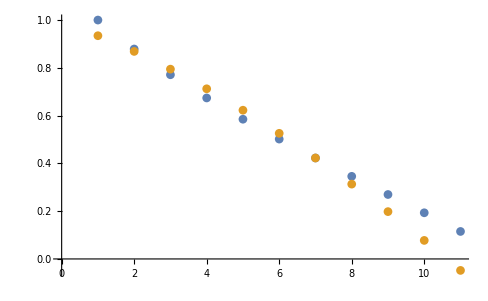

0.934451

```mathematica
ListPlot[{Table[Subscript[y, i],{i,0,10}],Table[Subscript[z, i],{i,0,10}]}]
Print[Subscript[z, 0]];
```